-53.8503+0.00106898 x

0.933709-0.0000347738 x+1.26724×10^-9 x^2

1.46243-0.0000567496 x+1.33337×10^-9 x^2-4.6366×10^-17 x^3

-3.14247+0.000234829 x-3.72062×10^-10 x^2+2.91292×10^-15 x^3-1.55504×10^-21 x^4

-1.65689+0.00041812 x-1.0197×10^-8 x^2+1.10428×10^-13 x^3-5.05429×10^-19 x^4+1.24266×10^-24 x^5-1.68957×10^-30 x^6+1.19325×10^-36 x^7-3.40375×10^-43 x^8

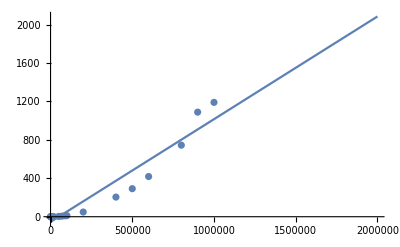

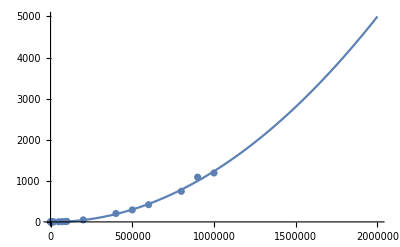

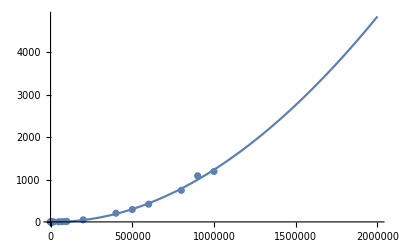

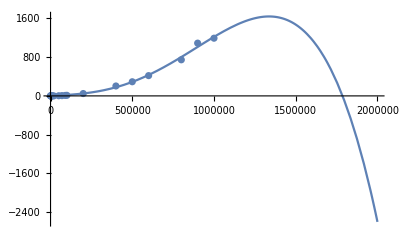

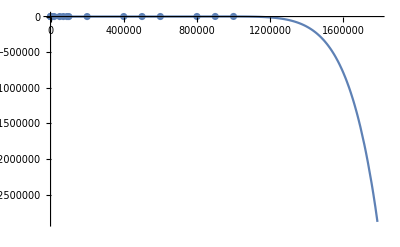

```mathematica
seleccion1=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x},x]

seleccion2=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2},x]

seleccion3=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3},x]

seleccion4=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3,x^4},x]

seleccion8=Fit[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

puntos=ListPlot[{{100,0.0000159740447998046},{500,0.000365019},{1000,0.001303196},{2000,0.005572081},{5000,0.038476944},{8000,0.080535173},{9000,0.198409081},{10000,0.127197027},{20000,0.48895812},{50000,2.950371981},{70000,5.861546993},{90000,9.651067972},{100000,11.82698393},{200000,48.65380311},{400000,204.3738148},{500000,291.7892001},{600000,418.247813},{800000,744.585923},{900000,1088.344782},{1000000,1190.107606}}]

g1=Plot[seleccion1,{x,0,2000000}]
Show[puntos,g1,PlotRange->All]

g2=Plot[seleccion2,{x,0,2000000}]
Show[puntos,g2,PlotRange->All]

g3=Plot[seleccion3,{x,0,2000000}]
Show[puntos,g3,PlotRange->All]

g4=Plot[seleccion4,{x,0,2000000}]
Show[puntos,g4,PlotRange->All]

g8=Plot[seleccion8,{x,0,2000000}]
Show[puntos,g8,PlotRange->All]
```